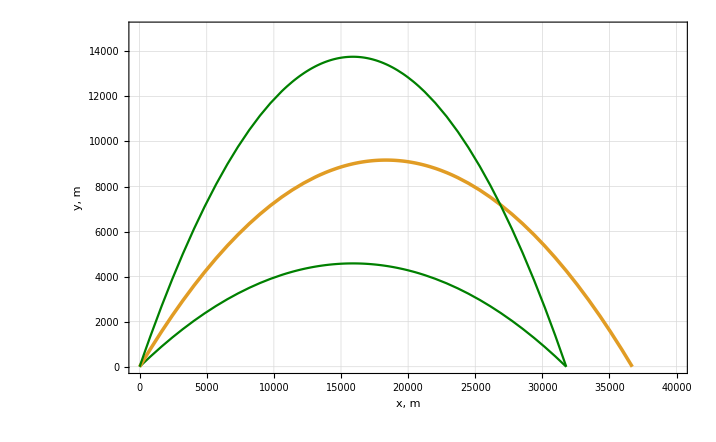

```mathematica
x4=Plot [Evaluate[Table[x Tan[n*π*15/180]-(x^2*9.81)/((Cos[n*π*15/180])^2*2*600^2),{n,2,4}]],{x,0,40000},PlotStyle->{RGBColor["Green"],Thickness[0.0035]},FrameStyle->Directive[Black,20],Frame->True,FrameLabel->{Style["x, m",24,Black,FontFamily->"Cambria"],Style["y, m",24,Black,FontFamily->"Cambria"]},GridLines->Automatic ,GridLinesStyle->Directive[Gray,Dashed],PlotRange->{{0,40000},{0,15000}}];
x5=Plot [25-x^2/(100),{x,-120,120},PlotStyle->{RGBColor["#e3e3e3"],Thickness[0.0035]},FrameStyle->Directive[Black,20],Frame->True,FrameLabel->{Style["",30,Black,FontFamily->"Cambria"],Style["",30,Black,FontFamily->"Cambria"]},GridLines->Automatic ,GridLinesStyle->Directive[Gray,Dashed],PlotRange->{{-55,55},{0,27}}, Filling->Axis];

Show[x4]
```